```mathematica
raw = Import["~/results.json"];
raw = Association[#]&/@raw;
raw[[1]]
```

<|energyGeV→9.94002,Q19851→-64.0952,Q19871→44.9361,x801→0.00010383,x901→0.0000401003,xM1E→-0.000760351,xM11E→-0.000683843,xM1FF→0.000106716,xM2FF→0.00014227|>

```mathematica
(*Sometimes BPMs get zeros. Toss*)
Length[raw]
raw = Select[ raw, AllTrue[#,#!=0&]& ];
Length[raw]
```

1000

997

## Sanity check dispersion

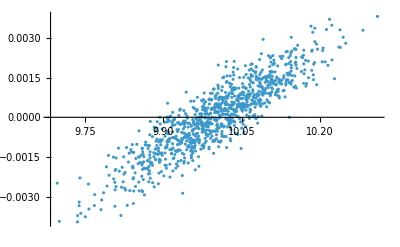

```mathematica
ListPlot[{#energyGeV,#xM1E}&/@raw]
```

```mathematica
nlm=NonlinearModelFit[
{(#energyGeV)/(10*^9),#xM1E}&/@raw,
m x + b,
{m,b},
x
]
```

FittedModel[…]

```mathematica
nlm["BestFitParameters"]
```

{m→1.21763×10^8,b→-0.121739}

-Graphics-

Good to a percent or so...

## Other testing

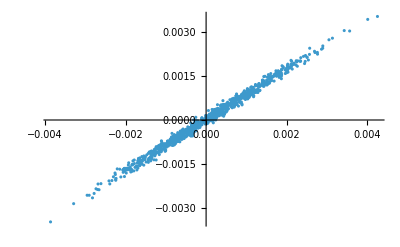

```mathematica
ListPlot[{#x801,#x901}&/@raw]
```

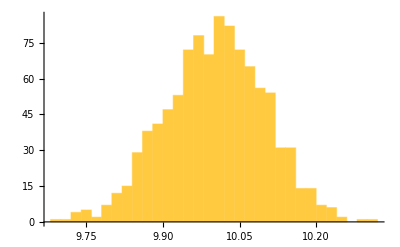

```mathematica
Histogram[raw[[All,"energyGeV"]],20]
```

```mathematica
MinMax[raw[[All,"energyGeV"]]]
```

{9.69716,10.3095}

```mathematica
Export[
"~/SRdump.csv",
Tabular[raw]
]
```

~/SRdump.csv

```mathematica
10 + 79.7 * 0.001
```

10.0797

```mathematica
(10.0797/10) * 0.12
```

0.120956

## Check SR

### Upstream

Bmad gives the dispersion at M1E as 0.120 m

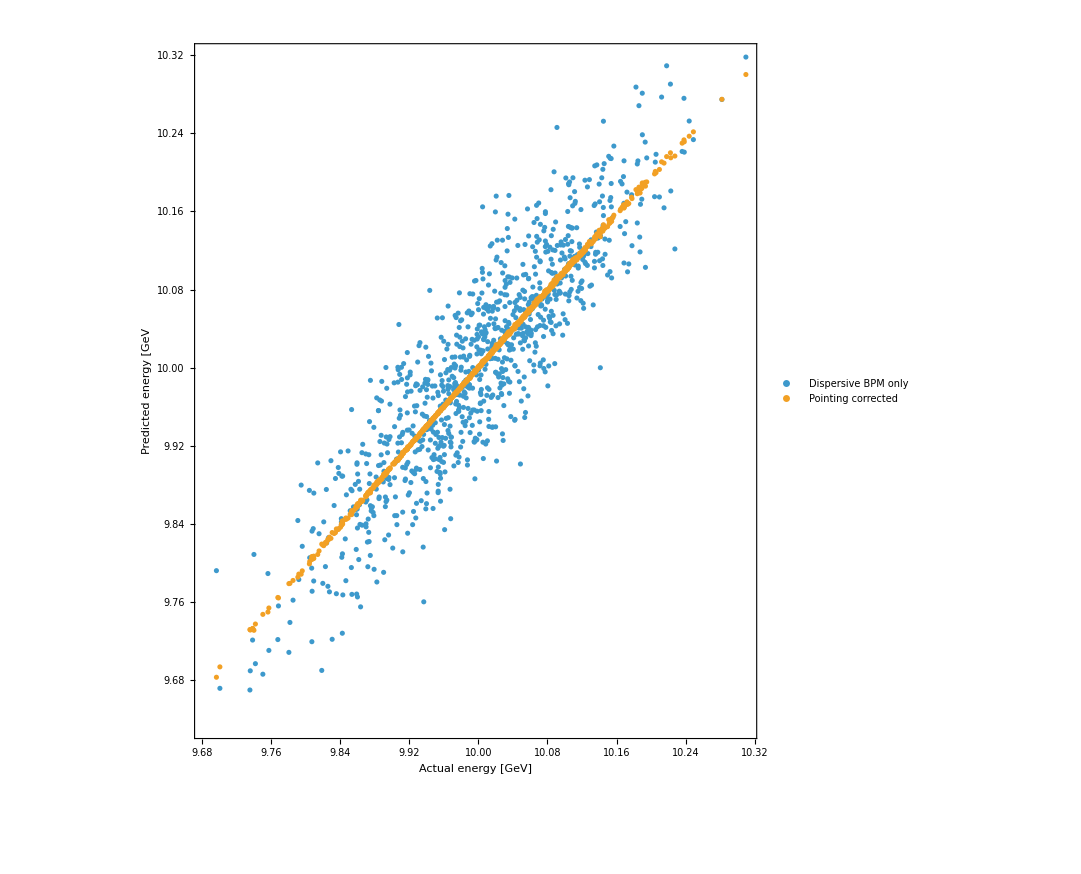

```mathematica
ListPlot[{
{
#energyGeV,
(#xM1E / 0.120)*10+10
}&/@raw
,

{
#energyGeV,
10+0.08260*(1000*#x801-1.73*1000*#x901+1000*#xM1E)
}&/@raw

},



ImageSize->800,
LabelStyle->20,
Frame->True,
FrameLabel->{"Actual energy [GeV]", "Predicted energy [GeV" },
PlotLegends->Placed[{"Dispersive BPM only", "Pointing corrected"},{0.8,0.1}],
AspectRatio->Automatic
]
```

### Downstream

Bmad gives the dispersion at M11E as 0.120 m

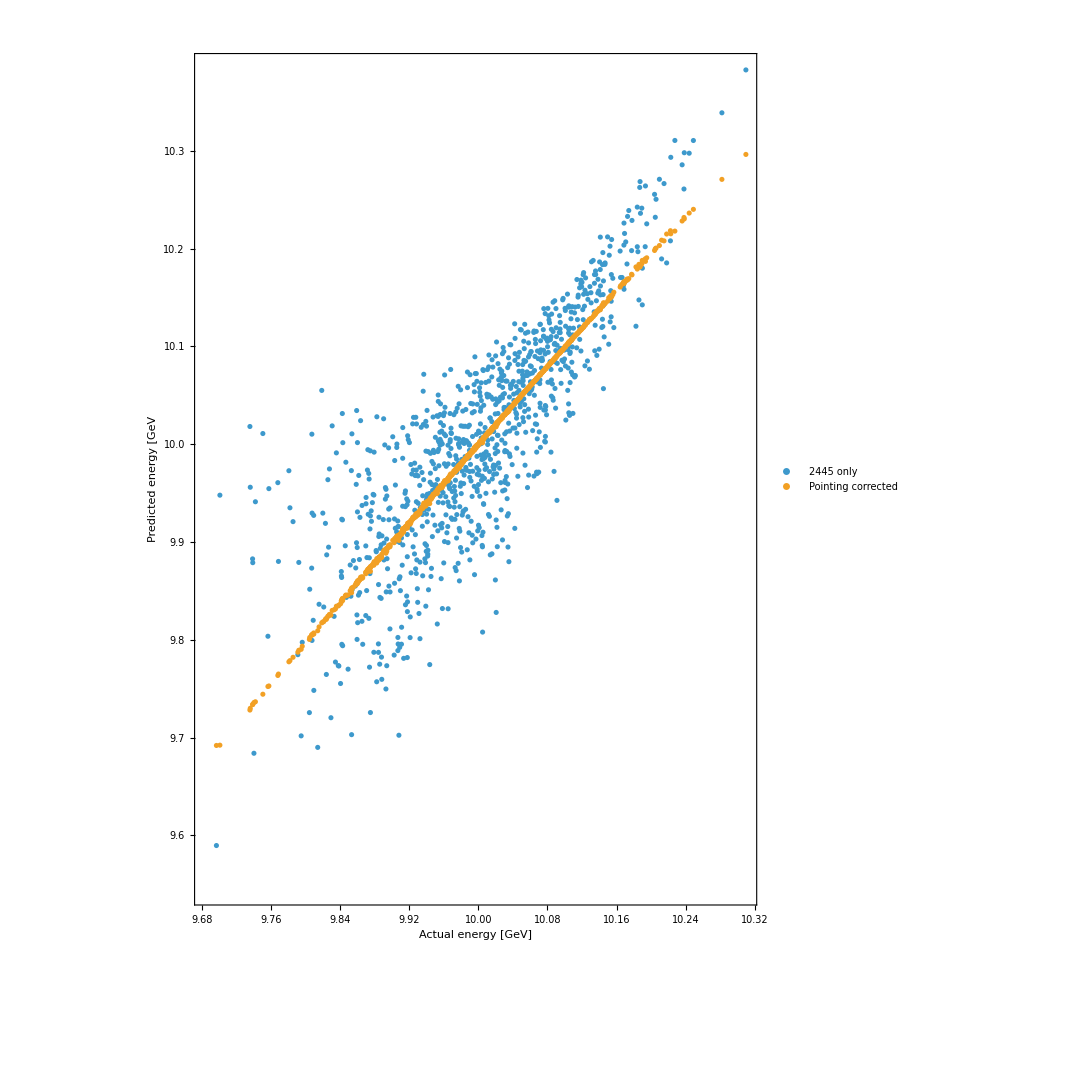

```mathematica
ListPlot[{
{
#energyGeV,
(#xM11E / 0.120)*10+10
}&/@raw
,

{
#energyGeV,
10 +0.0834 * ( 1000*#xM11E + 7.58 * ( 0.813 * #xM2FF * 1000 - #xM1FF * 1000) - #xM1FF * 1000)
}&/@raw

},



ImageSize->800,
LabelStyle->20,
Frame->True,
FrameLabel->{"Actual energy [GeV]", "Predicted energy [GeV" },
PlotLegends->Placed[{"2445 only", "Pointing corrected"},{0.8,0.1}],
AspectRatio->Automatic
]
```